```mathematica
a[x_Integer]:= 2*a[x-1] - (x-1) //N
```

```mathematica
a[0] = 2;
```

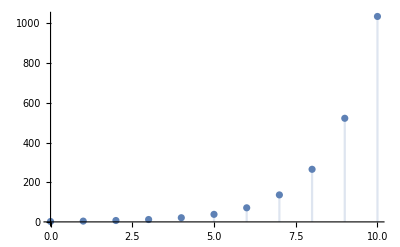

```mathematica
h1 = DiscretePlot[a[n], {n, 0, 10}]
```

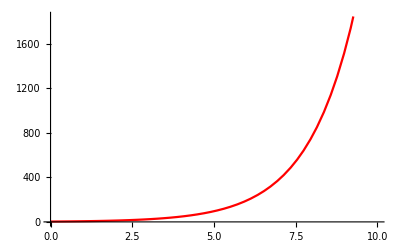

```mathematica
h2 = Plot[2^x * 3, {x, 0, 10}, PlotStyle->Red]
```

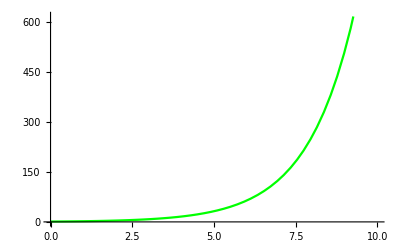

```mathematica
h3 = Plot[2^x, {x, 0, 10}, PlotStyle->Green]
```

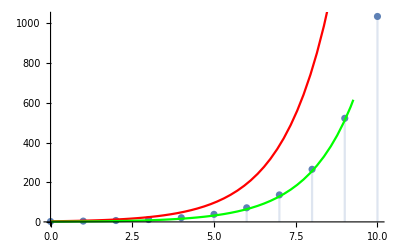

```mathematica
Show[h1,h2, h3]
```

```mathematica
ListLogPlot[a[n], {n, 0, 10}]
```

ListLogPlot::nonopt: Options expected (instead of {n,0,10}) beyond position 1 in ListLogPlot[a[n],{n,0,10}]. An option must be a rule or a list of rules.

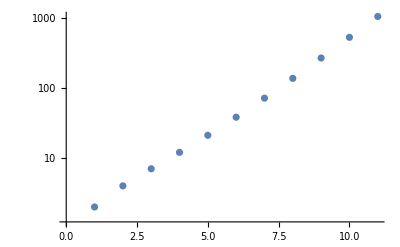

```mathematica
g1= ListLogPlot[Table[a[n],{n,0,10}]]
```

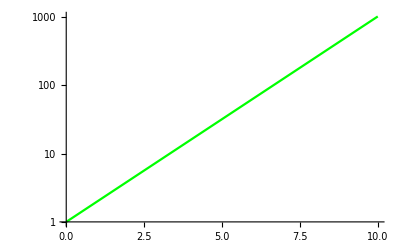

```mathematica
g2 = LogPlot[2^x, {x, 0, 10}, PlotStyle->Green]
```

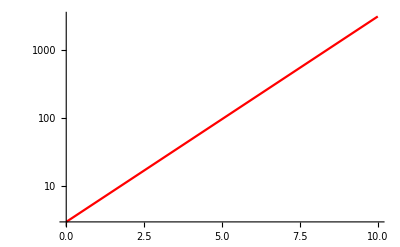

```mathematica
g3 = LogPlot[2^x * 3, {x, 0, 10}, PlotStyle->Red]
```

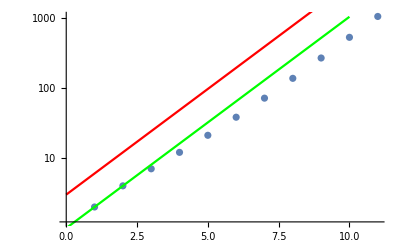

```mathematica
Show[g1,g2,g3]
```

```mathematica
Manipulate[Show[g1, LogPlot[Exp[x/a], {x,1,100}]], {a,1,3}]
```

```mathematica
b[x_Integer]:=(1+1/x)^(x+1)-ⅇ
```

```mathematica
Clear[c]
```

```mathematica
Clear[n]
```

```mathematica
RecurrenceTable[{c[n]==(1+1/n)^(n+1), c[1]==4},c[n], {n,2,100}]
```

RecurrenceTable[{c[n]==(1+1/n)^(1+n),c[1]==4},c[n],{n,2,100}]

```mathematica
(*5, x->1*)
```

```mathematica
f[x_]:=(ⅇ^(x-1)-1)/(x^2-1)
```

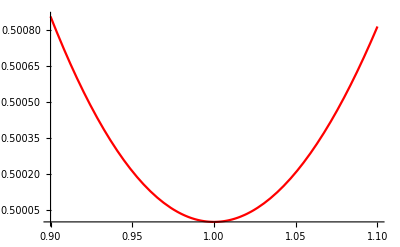

```mathematica
d1= Plot[f[x], {x, 0.9, 1.1}, PlotStyle->Red]
```

```mathematica
Manipulate[Show[d1,Plot[a, {x, 0.9, 1.1}]], {a, 0.4999, 0.5002}]
```

Show::gcomb: Could not combine the graphics objects in Show[0.901982,].

```mathematica
Clear[b]
```

```mathematica
b = Limit[f[x], x->1]
```

1/2

```mathematica
Reduce[{f[x]-b < 0.1, f[x]-b>-0.1},x,Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0980176<x<1.||1.<x<2.17537

```mathematica
d1 = 1-0.0980175845054051;
```

```mathematica
d2 = 2.175369210894916 - 1;
```

```mathematica
δ = Min[d1,d2]
```

0.901982

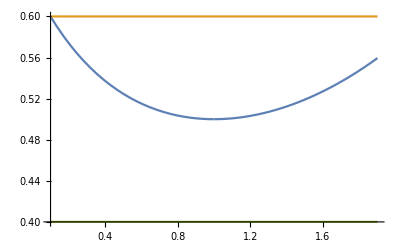

```mathematica
Plot[{f[x], b+0.1, b-0.1}, {x,1-δ, 1+δ}]
```

```mathematica
Сlear[b]
```

Сlear[1/2]

```mathematica
Clear[x]
```

```mathematica
b[x_Integer]:=(1+1/x)^(x+1)-ⅇ
```

SetDelayed::write: Tag Rational in 1/2[x_Integer] is Protected.

$Failed

```mathematica
Clear[n, h1, h2,h3]
```

```mathematica
r[n_]:=(1+1/n)^(n+1)-ⅇ
```

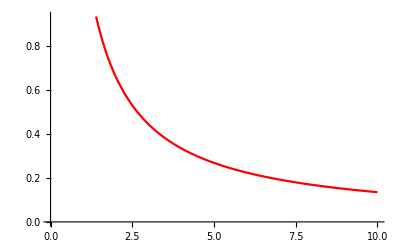

```mathematica
h1 = Plot[r[n], {n, 1, 10}, PlotStyle->Red, AxesOrigin->{0,0}]
```

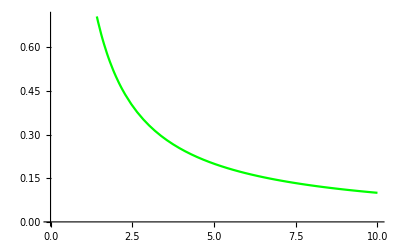

```mathematica
h2 = Plot[1/x, {x, 1, 10}, PlotStyle->Green, AxesOrigin->{0,0}]
```

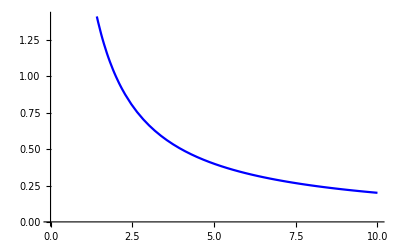

```mathematica
h3 = Plot[2/x, {x, 1, 10}, PlotStyle->Blue, AxesOrigin->{0,0}]
```

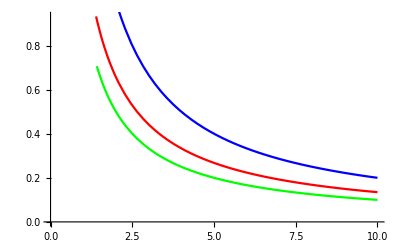

```mathematica
Show[h1,h2, h3]
```

```mathematica
Manipulate[Show[h1, Plot[a/x, {x, 1,10}]], {a,1,2}]
```

```mathematica
(*Гипотеза: заданнфя функция стремится к своему пределу быстрее, чем 2/x b межденнее, чем 1/x. так же,  примерное равенство появляется при значении аргумента числителя (a/x) a= 1.312. Все доказательства приведены на графиках выше*)
```